{800,2}

d+1/2 ((2 eta^2 (n+1) omega t sin(2 omega t)+cos(2 omega t))/(4 eta^4 (n+1)^2 omega^2 t^2+1)+1)

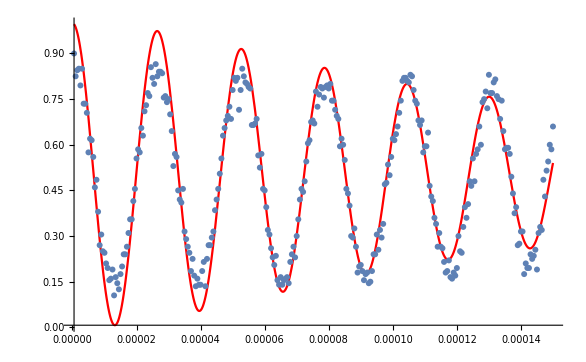

{omega→124641.,n→6.18086,d→-0.0084988}

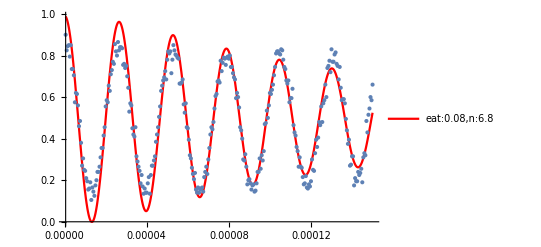

25.2051

```mathematica
ClearAll[dirname,filename,data,data2];
file="D:\\Document\\Seafile\\Experiment\\Artiq\\Sequence\\repository\\data\\RabiTime-2021-05-14-21-26.csv";
data=Import[file];
Dimensions[data]
data[[;;,1]]=data[[;;,1]]/10^6;
data[[;;,2]]=data[[;;,2]]/200;
data2=data[[1;;300, ;;2]];

Clear[omega,n,t,eta,d];
expr=1/2 (1+(Cos[2 omega t]+2 omega t eta^2 (n+1) Sin[2 omega t])/(1+(2 omega t eta^2 (n+1))^2))+d;
TraditionalForm[expr]
xdata=Transpose[data2][[1]];
test={omega->Pi/(25.2051/10^6),n->7,eta->0.08,d->0.00};
Show[Plot[expr/.test,{t,Min[xdata],Max[xdata]},PlotRange->Full,PlotStyle->Red],ListPlot[data2,PlotRange->Full]]

expr2=1/2 (1+(Cos[2 omega t]+2 omega t eta^2 (n+1) Sin[2 omega t])/(1+(2 omega t eta^2 (n+1))^2))+d/.{eta->0.087};
fitresult=FindFit[data2,expr2,{{omega,Pi/(25/10^6)},{n,5},{d,0.00}},t,MaxIterations->10000]
Show[Plot[expr2/.fitresult,{t,Min[xdata],Max[xdata]},PlotRange->Full,PlotStyle->Red,PlotLegends->{"eat:0.08,n:6.8"}],ListPlot[data2,PlotRange->Full]]
Pi/(10^-6 omega)/.fitresult
```

```mathematica
□
```

25.2051